***** Warning ! *****
BaseIO: redefining field speed.
********************
Field arrayOrdering defaults to Reversed
Field origin defaults to {0,0}
Field sndOrder defaults to 0
Fast marching solver completed in 0.000466 s.
Field exportActiveNeighs defaults to 0
Field exportGeodesicFlow defaults to 0
Unused fields from compute : MaxStencilWidth StencilCPUTime nAccepted 
Defaulted fields : arrayOrdering exportActiveNeighs exportGeodesicFlow origin sndOrder

{False,True}

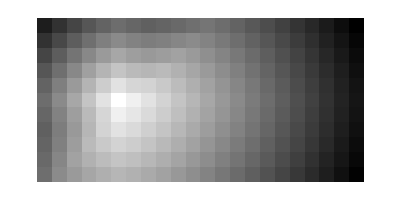

```mathematica
Module[{params=Association[{}],n=11,values,test,used,defaulted},
hfmLibraryPath=FileNameJoin[{hfmBinDirectory,"libMathematicaHFM_Isotropic"}]; 
params["model"]="IsotropicBox2<Boundary::Closed>";
params["speed"]=Array[1.&,{2n,n}];
params["dims"]={2n,n};
params["gridScale"]=1./n;
params["seeds"]={{0.5,0.5}};
params["exportValues"]=1.;

LoadHFMWLL[hfmLibraryPath];
hfmSetVariable[#1,#2]&@@@Normal[params];
hfmSetVariable["speed",Array[If[#1>#2,2.,1.]&,{2n,n}]];
hfmSetVariable["verbosity",2];
hfmRunModel[];
values=hfmGetArray[2]["values"];
Print[hfmHasField/@{"Hi","MaxStencilWidth"}];
hfmEraseField["FMCPUTime"];
UnloadHFMWLL[];
TablePlot[values]
]
```